## Pristine ZrC electron transport;

```mathematica
Some basic information;
```

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
```

```mathematica
Import data;
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRates=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

```mathematica
ListPlot[Transpose[{Transpose[scatteringRates[[1]]][[3]],Transpose[scatteringRates[[1]]][[5]]}],PlotRange->{All,{0,3*10^-9}}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Transpose[scatteringRates[[1]]][[3]],Transpose[scatteringRates[[1]]][[4]]}]]
```

-Graphics-

```mathematica
ListPlot[Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[scatteringRates[[i]]][[4]]}],{i,2,11,3}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,2,11,3}]],Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"}]
```

-Graphics-

```mathematica
dataThin1000=Table[data[[i]],{i,1,data//Length,1000}];
dataThin100=Table[data[[i]],{i,1,data//Length,100}];
```

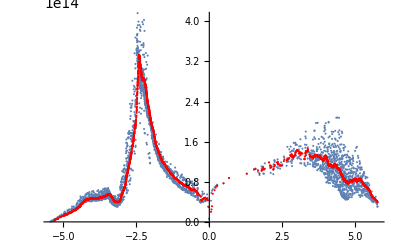

```mathematica
Show[{ListPlot@dataThin100,ListPlot[MovingMap[GeometricMean,{dataThin100},0.11],PlotStyle->Red]}]
```

```mathematica
dataGP=Flatten[{#1->#2}&@@@dataThin1000];
```

```mathematica
p=Predict[dataGP,Method->"GaussianProcess"];
```

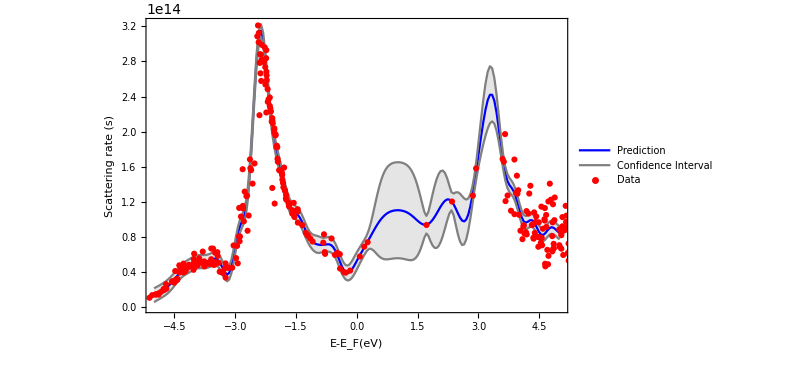

```mathematica
Show[Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600],ListPlot[List@@@dataGP,PlotStyle->Red,PlotLegends->{"Data"}]]
```

```mathematica
dataRand=RandomSample[data,500];
```

```mathematica
dataGPRand=Flatten[{#1->#2}&@@@dataRand];
```

```mathematica
p=Predict[dataGPRand,Method->"GaussianProcess"];
```

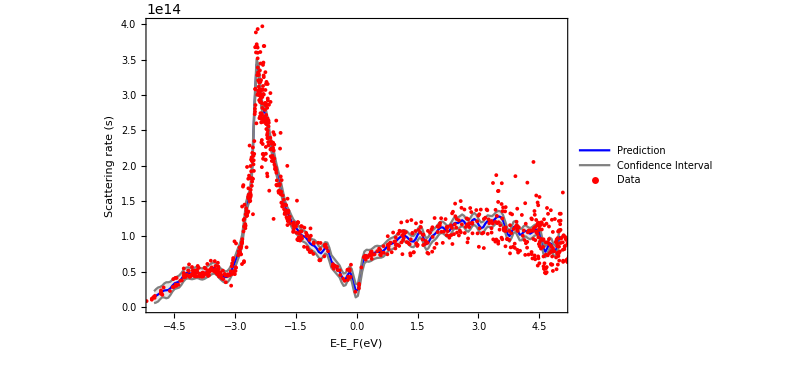

```mathematica
Show[Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataGPRand,PlotStyle->Red,PlotLegends->{"Data"}]]
```

```mathematica
dataRand500=RandomSample[data,500];
dataGPRand500=Flatten[{#1->#2}&@@@dataRand500];
```

```mathematica
p500=Predict[dataGPRand500,Method->"GaussianProcess"];
```

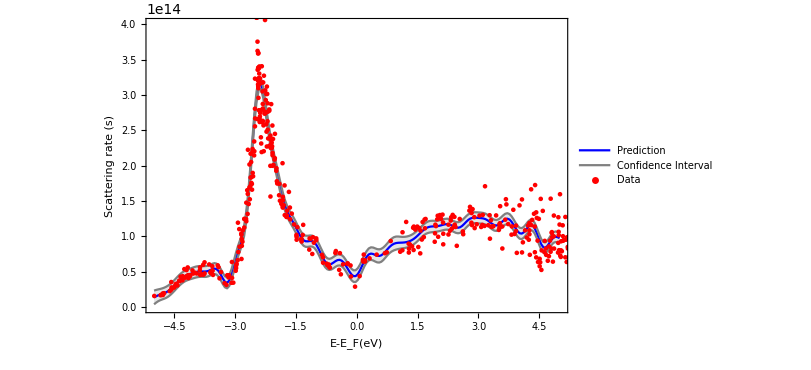

```mathematica
Show[Plot[{p500[x],p500[x]+StandardDeviation[p500[x,"Distribution"]],p500[x]-StandardDeviation[p500[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataGPRand500,PlotStyle->Red,PlotLegends->{"Data"}]]
```

```mathematica
dataRand250=RandomSample[data,250];
dataGPRand250=Flatten[{#1->#2}&@@@dataRand250];
```

```mathematica
p250=Predict[dataGPRand250,Method->"GaussianProcess"];
```

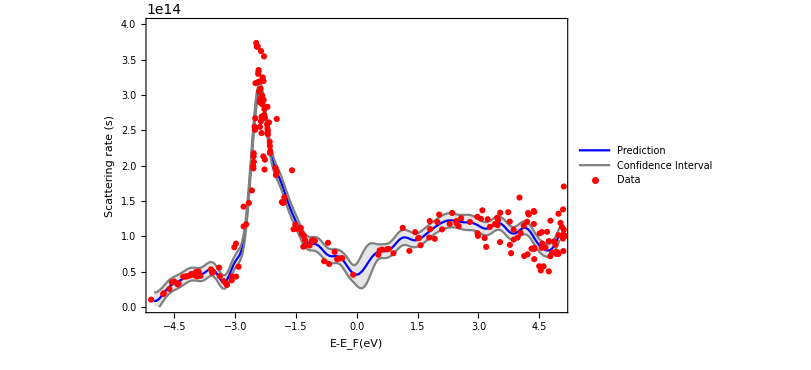

```mathematica
Show[Plot[{p250[x],p250[x]+StandardDeviation[p250[x,"Distribution"]],p250[x]-StandardDeviation[p250[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataGPRand250,PlotStyle->Red,PlotLegends->{"Data"}]]
```

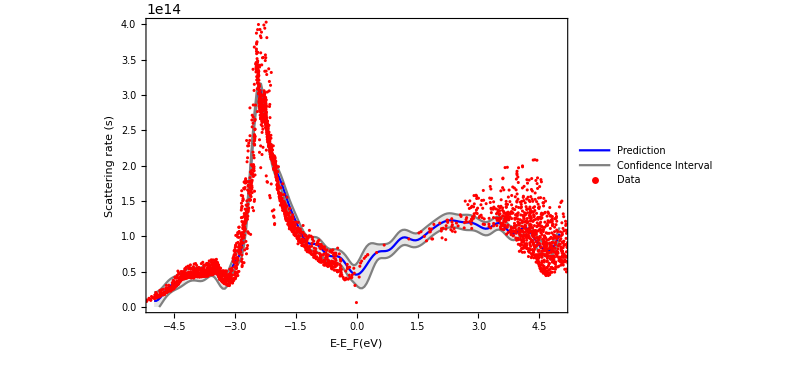

```mathematica
Show[Plot[{p250[x],p250[x]+StandardDeviation[p250[x,"Distribution"]],p250[x]-StandardDeviation[p250[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataThin100,PlotStyle->Red,PlotLegends->{"Data"}]]
```

```mathematica
dataRand1000=RandomSample[data,1000];
dataGPRand1000=Flatten[{#1->#2}&@@@dataRand1000];
```

```mathematica
p1000=Predict[dataGPRand1000,Method->"GaussianProcess"];
```

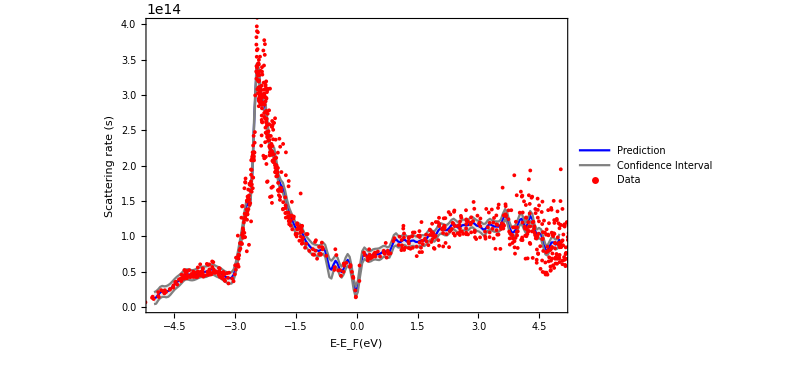

```mathematica
Show[Plot[{p1000[x],p1000[x]+StandardDeviation[p1000[x,"Distribution"]],p1000[x]-StandardDeviation[p1000[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataRand1000,PlotStyle->Red,PlotLegends->{"Data"}]]
```

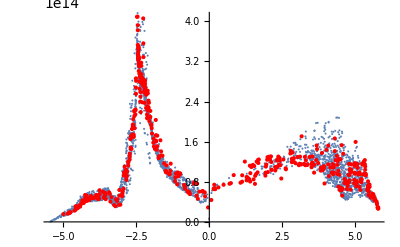

```mathematica
Show[{ListPlot@dataThin100,ListPlot[MovingMap[Mean,{dataRand500},0.01],PlotStyle->Red]}]
```

PredictorFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (x).

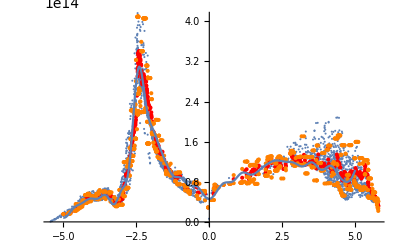

```mathematica
Show[{ListPlot@dataThin100,ListPlot[MovingMap[Mean,{dataRand500},0.1],PlotStyle->Red],ListPlot[MovingMap[Max,{dataRand500},0.1],PlotStyle->Orange],ListPlot[MovingMap[Min,{dataRand500},0.1],PlotStyle->Orange],Plot[p250[x]/.x->X,{X,-5,5},PlotRange->All]}]
```

PredictorFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (x).

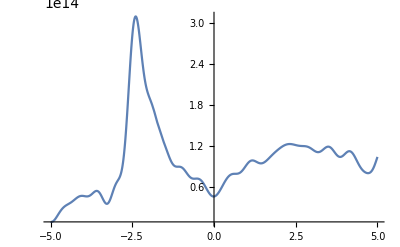

```mathematica
Plot[p250[x]/.x->X,{X,-5,5},PlotRange->All]
```

```mathematica
Off[PredictorFunction::mlincfttp]
NIntegrate[p250[x]/.x->X,{X,-5,5}]
```

NIntegrate::inumr: The integrand p250[X] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-5,5}}.

NIntegrate[p250[x]/.x→X,{X,-5,5}]

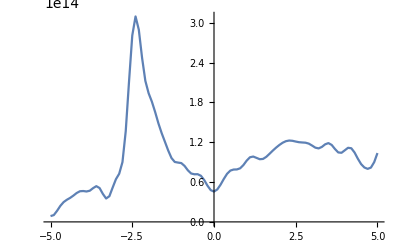

```mathematica
ListLinePlot[Table[{x,p250[x]},{x,-5,5,0.1}],PlotRange->All]
```

```mathematica
inter=Interpolation[Table[p250[x],{x,-5,5,0.1}]]
```

InterpolatingFunction[{{1., 101.}}, <>]

```mathematica
dataRand1000=RandomSample[data,30000];
```

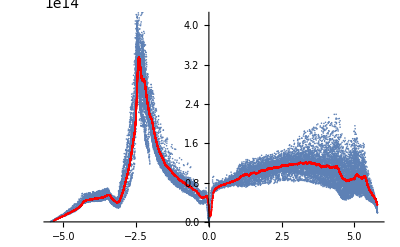

```mathematica
Show[{ListPlot@dataRand1000,ListPlot[MovingMap[Mean,{dataRand1000},{0.1}],PlotStyle->Red]}]
```

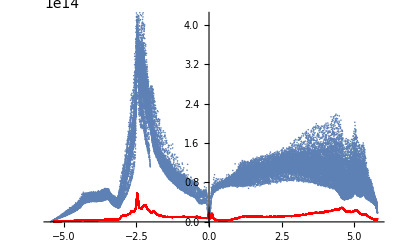

```mathematica
Show[{ListPlot@dataRand1000,ListPlot[MovingMap[MeanDeviation,{dataRand1000},{0.1}],PlotStyle->Red]}]
```

```mathematica
dataMM=MovingMap[Mean,{dataRand1000},{0.1}]
```

{{-5.34108,2.26571×10^12},{-5.33282,2.32378×10^12},{-5.33281,2.39842×10^12},{-5.33261,2.44815×10^12},{-5.32245,2.58049×10^12},{-5.31627,2.65196×10^12},{-5.31138,2.83779×10^12},29966,{5.7917,3.5193×10^13},{5.79288,3.50664×10^13},{5.79324,3.50373×10^13},{5.79379,3.49796×10^13},{5.79418,3.49212×10^13},{5.7944,3.48633×10^13},{5.79668,3.46172×10^13}}
 |  |  |  |

```mathematica
dataGPMM=Flatten[{#1->#2}&@@@dataMM];
```

```mathematica
pMM=Predict[dataGPMM,Method->"GaussianProcess"];
```

```mathematica
Show[Plot[{pMM[x],pMM[x]+StandardDeviation[pMM[x,"Distribution"]],pMM[x]-StandardDeviation[pMM[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@dataRand1000,PlotStyle->Red,PlotLegends->{"Data"}]]
```